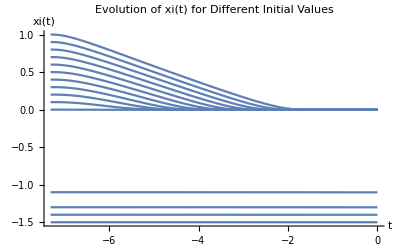

Solutions for xi[t] successfully generated.

Solutions for OmegaM[t] successfully generated.

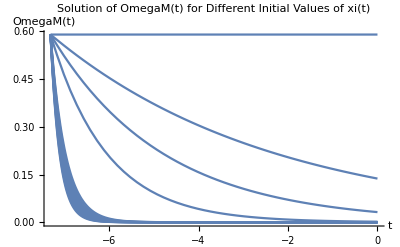

Solutions for xi[t] successfully generated.

Solutions for OmegaaR[t] successfully generated.

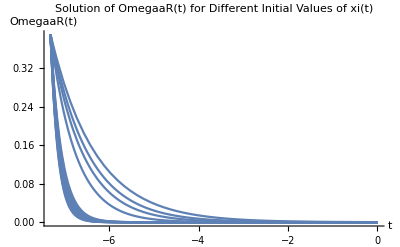

Solutions for OmegaM[t] and OmegaaR[t] successfully generated.

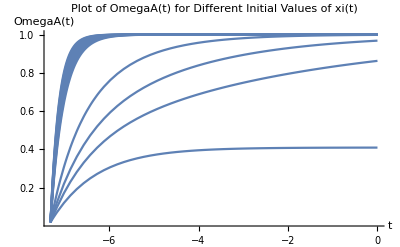

```mathematica
(*Clear previous definitions*)ClearAll[t,xi,alpha,n,OmegaR,sol,term1,term2,term3,term4,term5,term6,term7,term8,term9,term10,term11,term12,term13,term14,term15,diffEq];

(*Parameters*)
n= 1;
alpha=23;

(*Define the terms symbolically*)
term1=Exp[(4^n)*alpha*(((2+xi[t])*(6+5*xi[t])/((1+xi[t])*(3+xi[t])))^n)];
term2=-(3+2*xi[t]);
term3=-(2*(4^n)*n*alpha*xi[t]*((3+2*xi[t])^2))/((1+xi[t])*(6+5*xi[t]));
term4=((2+xi[t])*(6+5*xi[t])/((1+xi[t])*(3+xi[t])))^n;
term5=-(2*(4^n)*n*alpha)*term4;
term6=3*D[xi[t],t]/(((1+xi[t])^2)*((6+5*xi[t])^2)*((3+xi[t])^2));
term7=108+252*xi[t]+225*(xi[t]^2)+96*(xi[t]^3)+17*(xi[t]^4)+2*n*((3+2*xi[t])^2);
term8=2*n*((3+2*xi[t])^2)*(xi[t]^2)*(4^n)*alpha*term4;
term9=(D[xi[t],t]^2)/(((1+xi[t])^3)*((2+xi[t])^2)*((3+xi[t])^3)*((6+5*xi[t])^3));
term10=-9720-388556*xi[t]-65070*(xi[t]^2)-61371*(xi[t]^3)-35532*(xi[t]^4)-12834*(xi[t]^5)-2782*(xi[t]^6)-255*(xi[t]^7);
term11=(-12*n*xi[t]*(2+xi[t])*(3+2*xi[t])*(-27-36*xi[t]+15*(xi[t]^3)+5*(xi[t]^4)))*(1+(4^n)*alpha*term4);
term12=4*(n^2)*(xi[t]^3)*((3+2*xi[t])^3);
term13=1+(2^n)*alpha*(3*(2^n)*term4+(8^n)*alpha*(((2+xi[t])*(6+5*xi[t])/((1+xi[t])*(3+xi[t])))^(2*n)));
term14=D[xi[t],{t,2}]/(((1+xi[t])^2)*(2+xi[t])*((3+xi[t])^2)*((6+5*xi[t])^2));
term15=(108+252*xi[t]+225*(xi[t]^2)+96*(xi[t]^3)+17*(xi[t]^4))+2*n*xi[t]*((3+xi[t])^2)*(1+(4^n)*alpha*term4);

OmegaR=term1*(term2+term3*term4+term5*(term6*(term7+term8)+term9*(term10+term11+term12*term13)+term14*term15));

(*Differentiate OmegaR with respect to t*)
omegaRPrime=D[OmegaR,t];

(*The differential equation*)
diffEq=omegaRPrime+OmegaR*(4+2*xi[t])==0;
(*List of initial values for xi*)initialValues={-1.5,-1.4,-1.1,0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,-1.3};
(*Solve and plot for each initial value*)solutions=Table[NDSolve[{diffEq,xi[-7.31]==xi0,Derivative[1][xi][-7.31]==0,Derivative[2][xi][-7.31]==0},xi,{t,-7.31,0},Method->{"StiffnessSwitching"},MaxStepFraction->0.0001],{xi0,initialValues}];

(*Plot xi(t) solutions*)
plotsXi=Table[Plot[Evaluate[xi[t]/.sol],{t,-7.31,0},PlotRange->All],{sol,solutions}];

Show[plotsXi,PlotLabel->"Evolution of xi(t) for Different Initial Values",AxesLabel->{"t","xi(t)"}]








(*Check if solutions are correctly generated*)If[Length[solutions]==0,Print["No solutions generated for xi[t]."],Print["Solutions for xi[t] successfully generated."]];

(*Define the differential equation for OmegaM using the solution for xi[t]*)
OmegaMPrime=D[OmegaM[t],t];
OmegaMSolutions=Table[NDSolve[{OmegaMPrime+OmegaM[t]*(3+2*Evaluate[xi[t]/.solutions[[i]]])==0,OmegaM[-7.31]==0.59},OmegaM,{t,-7.31,0},Method->{"StiffnessSwitching"},MaxStepFraction->0.0001],{i,Length[solutions]}];

(*Check if OmegaM solutions are correctly generated*)
If[Length[OmegaMSolutions]==0||!AllTrue[OmegaMSolutions,(Length[#]>0&)],Print["No solutions generated for OmegaM[t]."],Print["Solutions for OmegaM[t] successfully generated."]];

(*Plot the solution OmegaM[t] for each xi[t]*)
plotsOmegaM=Table[Plot[Evaluate[OmegaM[t]/.OmegaMSolutions[[i]]],{t,-7.31,0},PlotRange->All,PlotLabel->"Solution of OmegaM(t)",AxesLabel->{"t","OmegaM(t)"}],{i,Length[OmegaMSolutions]}];

(*Combine the plots*)
If[Length[plotsOmegaM]>0,Show[plotsOmegaM,PlotLabel->"Solution of OmegaM(t) for Different Initial Values of xi(t)",AxesLabel->{"t","OmegaM(t)"}],Print["No plots to display."]]







(*Calculation of omegar and it's plot*)

(*Check if solutions are correctly generated*)If[Length[solutions]==0,Print["No solutions generated for xi[t]."],Print["Solutions for xi[t] successfully generated."]];

(*Define the differential equation for OmegaaR using the solution for xi[t]*)
OmegaaRPrime=D[OmegaaR[t],t];
OmegaaRSolutions=Table[NDSolve[{OmegaaRPrime+OmegaaR[t]*(4+2*Evaluate[xi[t]/.solutions[[i]]])==0,OmegaaR[-7.31]==0.39},OmegaaR,{t,-7.31,0},Method->{"StiffnessSwitching"},MaxStepFraction->0.0001],{i,Length[solutions]}];

(*Check if OmegaaR solutions are correctly generated*)
If[Length[OmegaaRSolutions]==0||!AllTrue[OmegaaRSolutions,(Length[#]>0&)],Print["No solutions generated for OmegaaR[t]."],Print["Solutions for OmegaaR[t] successfully generated."]];

(*Plot the solution OmegaaR[t] for each xi[t]*)
plotsOmegaaR=Table[Plot[Evaluate[OmegaaR[t]/.OmegaaRSolutions[[i]]],{t,-7.31,0},PlotRange->All,PlotLabel->"Solution of OmegaaR(t)",AxesLabel->{"t","OmegaaR(t)"}],{i,Length[OmegaaRSolutions]}];

(*Combine the plots*)
If[Length[plotsOmegaaR]>0,Show[plotsOmegaaR,PlotLabel->"Solution of OmegaaR(t) for Different Initial Values of xi(t)",AxesLabel->{"t","OmegaaR(t)"}],Print["No plots to display."]]













(*Check that both OmegaM and OmegaaR solutions were generated correctly*)If[Length[OmegaMSolutions]>0&&Length[OmegaaRSolutions]>0,Print["Solutions for OmegaM[t] and OmegaaR[t] successfully generated."],Print["No solutions generated for OmegaM[t] or OmegaaR[t]."]];

(*Plot 1-OmegaM(t)-OmegaaR(t) for each solution*)
plotsCombined=Table[Plot[Evaluate[1-(OmegaM[t]/.OmegaMSolutions[[i]])-(OmegaaR[t]/.OmegaaRSolutions[[i]])],{t,-7.31,0},PlotRange->All,PlotLabel->"Plot of 1 - OmegaM(t) - OmegaaR(t)",AxesLabel->{"t","1 - OmegaM(t) - OmegaaR(t)"}],{i,Length[OmegaMSolutions]}];

(*Combine the plots*)
If[Length[plotsCombined]>0,Show[plotsCombined,PlotLabel->"Plot of OmegaA(t) for Different Initial Values of xi(t)",AxesLabel->{"t","OmegaA(t)"}],Print["No plots to display."]]
```